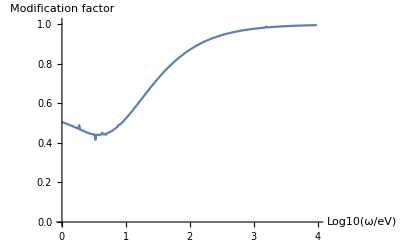

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];


omegaVal={};

lowerBound =0;
upperBound =4;
step =0.015;

t = Table[


(*Параметры АЛП*)
ω=10^(k);
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля*)
angle = Pi/3;
BSurf = 2*10^14;
R0 = 12;
period =3;

(*Размер области, должен быть равен радиусу*)
startingPoint = R0;

(*Радиус светового цилиндра*)
upperLimit=47713*period;


(*Значения поля (диполь)*)
bRep={bRad->BSurf*Cos[angle]*(R0/(x+startingPoint))^3,
	bTheta->0.5*BSurf*Sin[angle]*(R0/(x+startingPoint))^3,
	bPhi->0};

(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaPlasma:=3.1*10^(-12)*(bRad*Cos[angle]-bTheta*Sin[angle])*(1/period)*(1/ω);

deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
r[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)r0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};



(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ r'[x]==r[x].mat-mat.r[x]},r0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];
Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]
,{k,lowerBound,upperBound,step}];

(*Строим график*)
data=Transpose[{Range[lowerBound,upperBound,step],t}];
plot = ListLinePlot[data,PlotRange->{{lowerBound,upperBound},{0.0,1.01}},AxesLabel->{"Log10(ω/eV)","Modification factor"}, PlotMarkers->None]
(*AbsoluteTime[]-time*)

(*Обычная шкала*)
(*dataToFile = Transpose[{10^x/.x->Range[lowerBound,upperBound,step],t}];*)

(*Логарифмическая шкала*)
dataToFile = Transpose[{Range[lowerBound,upperBound,step],t}];

Export["Mixing.dat",dataToFile,"Table"];
```

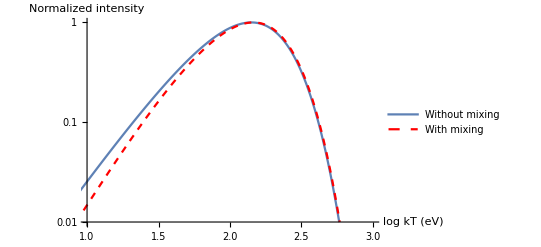

```mathematica
Clear["Global`*"]

(*Температура*)
T:=50;
T2:=48;

(*Спектр ЧТ*)
Planck[w_]:=w^3/(4 Pi^3)/(Exp[w/T]-1);
Planck2[w_]:=w^3/(4 Pi^3)/(Exp[w/T2]-1);

(*Импорт данных*)
mixingResult = Import["Mixing.dat"];
energyLogValues=mixingResult[[All,1]];
energyValues = 10^x/.x->energyLogValues;
mixingValues = mixingResult[[All,2]];

(*Расчет спектра ЧТ*)
planckValues := Planck[energyValues]/Max[ Planck[energyValues]];
planckValues2 := Planck2[energyValues];

(*Нормализация*)

(*Расчет спектра со смешиванием*)
mixedPlanckValues=Planck[energyValues]*mixingValues/Max[Planck[energyValues]*mixingValues];



(*Вывод графиков, energyValues для обычной, energyLogValues для логарифмической*)
plotUnmixed = ListLogPlot[Transpose[{energyLogValues, planckValues}],
PlotRange->{{1,3},{0.01,1}},PlotLegends->{"Without mixing" },Joined->True];

plotMixed =  ListLogPlot[Transpose[{energyLogValues, mixedPlanckValues}],PlotStyle->{Red,Dashed},
PlotRange->{{1,3},{0.01,1}},PlotLegends->{"With mixing" },Joined->True];

Show[plotUnmixed,plotMixed, AxesLabel->{"log kT (eV)","Normalized intensity"} ]
```

```mathematica
10^(1.9)
```

79.4328